Importamos archivo de áreas y lo guardamos en la variable áreas.

NotebookDirectory nos devuelve la ruta del archivo .nb

```mathematica
NotebookDirectory[]
```

/home/carlos/Documentos/Programacion/MetNum-UV/Unidad 1/Clase 6/

Unimos la ruta con el nombre del archivo para obtener la ruta absoluta

```mathematica
rutaAreas = FileNameJoin[{NotebookDirectory[],"areas.dat"}]
```

/home/carlos/Documentos/Programacion/MetNum-UV/Unidad 1/Clase 6/areas.dat

Importamos el archivo

```mathematica
areas = Import[rutaAreas]
```

{{1.2667×10^-6},{8.1073×10^-7},{5.1886×10^-7},{2.0268×10^-7}}

Importen resistencias.dat

```mathematica
rutaResistencias = FileNameJoin[{NotebookDirectory[],"resistencias.dat"}]
```

/home/carlos/Documentos/Programacion/MetNum-UV/Unidad 1/Clase 6/resistencias.dat

```mathematica
resistencias = Import[rutaResistencias]
```

{{0.0187},{0.0215},{0.0337},{0.0871}}

Opción 1

```mathematica
areasModificadas = Flatten[areas]
```

{1.2667×10^-6,8.1073×10^-7,5.1886×10^-7,2.0268×10^-7}

Opción 2

```mathematica
First[Transpose[areas]]
```

{1.2667×10^-6,8.1073×10^-7,5.1886×10^-7,2.0268×10^-7}

```mathematica
resistenciasModificadas = Flatten[resistencias]
```

{0.0187,0.0215,0.0337,0.0871}

```mathematica
areasResistencias = Transpose[{areasModificadas,resistenciasModificadas}]
```

{{1.2667×10^-6,0.0187},{8.1073×10^-7,0.0215},{5.1886×10^-7,0.0337},{2.0268×10^-7,0.0871}}

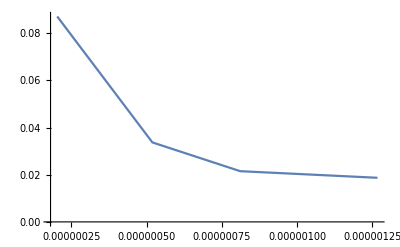

```mathematica
ListLinePlot[areasResistencias,PlotRange->All]
```

```mathematica
model = a*Exp[-k*x]+b;
```

```mathematica
ajuste = FindFit[areasResistencias,model,{a,b,k},x,Method->"Gradient",WorkingPrecision->50]
```

{a→1201.7703902887981545949580097959245699285231909055,b→-1201.6886239485135834407956250946561482294786801212,k→49.3707}

```mathematica
funcionAjustada = ReplaceAll[model,ajuste]
```

-1201.6886239485135834407956250946561482294786801212+1201.7703902887981545949580097959245699285231909055 ⅇ^(-49.3707 x)

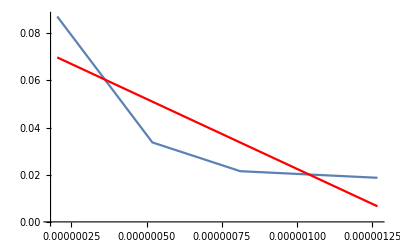

```mathematica
Show[
ListLinePlot[areasResistencias,PlotRange->All],
Plot[funcionAjustada,{x,1.2667*^-6,2.0268*^-7},PlotStyle->Red]
]
```

```mathematica
eval = Table[ReplaceAll[funcionAjustada,x->val],{val,areasResistencias[[All,1]]}]
```

{0.00661256,0.0336649,0.0509816,0.0697409}

```mathematica
MatrixForm[areasResistencias]
```

(1.2667×10^-6 | 0.0187
8.1073×10^-7 | 0.0215
5.1886×10^-7 | 0.0337
2.0268×10^-7 | 0.0871)

```mathematica
erroresRelativos = Abs[eval-areasResistencias[[All,2]]]/areasResistencias[[All,2]]
```

{0.646387,0.565809,0.512808,0.1993}

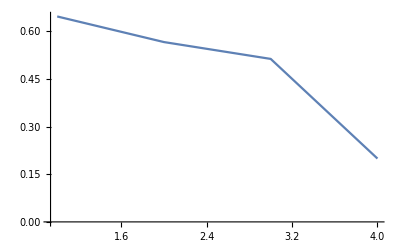

```mathematica
ListLinePlot[erroresRelativos,PlotRange->All]
```